Autor: Dawid Bitner

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 2

Metoda Adamsa-Bashfortha

Napisać procedurę realizującą algorytm trzy krokowej metody Adamsa-Bashfortha (argumenty:  f, x_0, y_0, b, n).
Zminimalizować liczbę obliczeń funkcji   f. Jako metodę startową wykorzystać metodę Rungego-Kutty rzędu trzeciego.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=((y(x))/x^2)^(1/3),  x∈[1,50],
y(1)=1.

Obliczenia wykonać dla 10, 20 i 50 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

```mathematica
func[x_, y_]:=(y/x^2)^(1/3);
```

```mathematica
(* Metoda Rungego-Kutty rzędu trzeciego *)
rk3[f_,x0_,y0_,h_,n_]:=Module[{x,y,results},
x = x0;
y = y0;
results = {{x,y}};
Do[
k1 = f[x,y];
k2 =f[x+1/2 h, y +1/2 h*k1];
k3 = f[x+h,y-h*k1+2h*k2];
x = x + h;
y = y + 1/6 h*(k1 + 4k2 + k3);
AppendTo[results, {x,y}];
,{i,1, n}];
Return [results];
];
```

```mathematica
(* Metoda Adamsa-Bashfortha  *)
ab[f_, x0_, y0_, b_,n_]:=Module[{
x,results,h,y,
k = 3.0
},
h = (b-x0)/n;
results = rk3[f, x0, y0, h, k];
tempF =Table[f[results⟦i,1⟧, results⟦i,2⟧], {i,Length[results]-k+1, Length[results]}];
Do[
y = Last[results]⟦2⟧+h*(tempF⟦3⟧*(23/12.)+tempF⟦2⟧*(-16/12.)+tempF⟦1⟧*(5/12.));
x = Last[results]⟦1⟧+h;
{tempF⟦1⟧, tempF⟦2⟧, tempF⟦3⟧} = {tempF⟦2⟧,tempF⟦3⟧, f[x,y]};
AppendTo[results, {x, y}];
,{i, k+1, n}
];

Return[results //N];
];
```

```mathematica
(* Rozwiązanie dokładne *)
result = DSolve[{yy'[x]==(yy[x]/x^2)^(1/3), yy[1]==1}, yy[x],x];
```

```mathematica
res = result⟦1,1,2⟧;
resultPlot = Plot[res, {x,1,50}, 
PlotStyle->{Black}, PlotLegends->LineLegend[{"Rozwiązanie dokładne"}]];
(* Rozwiązania Metodą Adamsa-Bashfortha *)
ab10 = ab[func, 1, 1, 50, 10];
ab20 = ab[func, 1, 1, 50, 20];
ab50 = ab[func, 1, 1, 50, 50];
```

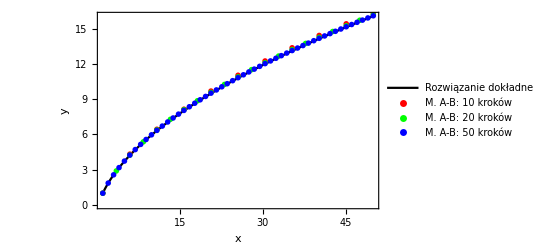

```mathematica
ab10Plot = ListPlot[ab10,PlotStyle->{PointSize[.01],Red}, PlotLegends->LineLegend[{"M. A-B: 10 kroków"}]];
ab30Plot = ListPlot[ab20,PlotStyle->{PointSize[.01],Green}, PlotLegends->LineLegend[{"M. A-B: 20 kroków"}]];
ab50Plot = ListPlot[ab50,PlotStyle->{PointSize[.01],Blue}, PlotLegends->LineLegend[{"M. A-B: 50 kroków"}]];
Show[resultPlot, ab10Plot, ab30Plot, ab50Plot, {Frame->True, FrameLabel->{"x", "y", "Metoda Adamsa-Bashfortha"}}]
```

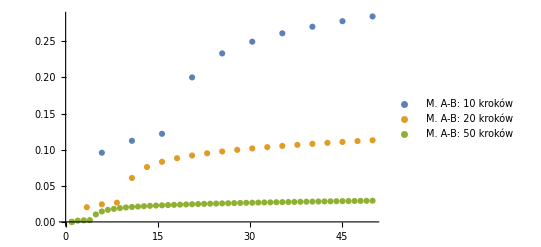

```mathematica
(* Błędy *)
error10 = Table[{ab10⟦i,1⟧, Abs[(res/.x->ab10⟦i,1⟧)-ab10⟦i,2⟧]},{i, 1, Length[ab10]}];
error20 = Table[{ab20⟦i,1⟧, Abs[(res/.x->ab20⟦i,1⟧)-ab20⟦i,2⟧]},{i, 1, Length[ab20]}];
error50 = Table[{ab50⟦i,1⟧, Abs[(res/.x->ab50⟦i,1⟧)-ab50⟦i,2⟧]},{i, 1, Length[ab50]}];
ListPlot[{error10, error20, error50},  PlotLegends->{LineLegend[{"M. A-B: 10 kroków", "M. A-B: 20 kroków", "M. A-B: 50 kroków"}]},
PlotRange->All]
```